```mathematica
(*Sedat Ekinci*)
<<NeuralNets`
```

```mathematica
trainingData=ExampleData[{"MachineLearning","FisherIris"},"TrainingData"];testData=ExampleData[{"MachineLearning","FisherIris"},"TestData"];
x=#[[1]]&/@trainingData

y=(#[[2]]/. {"setosa"->{1,0,0},"versicolor"->{0,1,0},"virginica"->{0,0,1}})&/@trainingData
```

{{4.7,3.2,1.3,0.2},{4.6,3.1,1.5,0.2},{5.,3.6,1.4,0.2},{5.4,3.9,1.7,0.4},{5.,3.4,1.5,0.2},{4.9,3.1,1.5,0.1},{5.4,3.7,1.5,0.2},{4.8,3.4,1.6,0.2},{4.8,3.,1.4,0.1},{5.7,4.4,1.5,0.4},{5.4,3.9,1.3,0.4},{5.4,3.4,1.7,0.2},{5.1,3.7,1.5,0.4},{4.6,3.6,1.,0.2},{5.1,3.3,1.7,0.5},{4.8,3.4,1.9,0.2},{5.,3.,1.6,0.2},{5.,3.4,1.6,0.4},{5.2,3.5,1.5,0.2},{4.7,3.2,1.6,0.2},{4.8,3.1,1.6,0.2},{5.4,3.4,1.5,0.4},{5.2,4.1,1.5,0.1},{4.9,3.1,1.5,0.2},{5.,3.2,1.2,0.2},{5.5,3.5,1.3,0.2},{4.9,3.6,1.4,0.1},{4.4,3.,1.3,0.2},{5.,3.5,1.3,0.3},{4.4,3.2,1.3,0.2},{5.,3.5,1.6,0.6},{5.1,3.8,1.9,0.4},{4.6,3.2,1.4,0.2},{5.3,3.7,1.5,0.2},{5.,3.3,1.4,0.2},{7.,3.2,4.7,1.4},{6.4,3.2,4.5,1.5},{6.9,3.1,4.9,1.5},{5.5,2.3,4.,1.3},{6.5,2.8,4.6,1.5},{6.3,3.3,4.7,1.6},{4.9,2.4,3.3,1.},{6.6,2.9,4.6,1.3},{5.2,2.7,3.9,1.4},{5.9,3.,4.2,1.5},{6.,2.2,4.,1.},{6.7,3.1,4.4,1.4},{5.6,3.,4.5,1.5},{5.6,2.5,3.9,1.1},{6.3,2.5,4.9,1.5},{6.1,2.8,4.7,1.2},{6.6,3.,4.4,1.4},{6.8,2.8,4.8,1.4},{6.7,3.,5.,1.7},{5.7,2.6,3.5,1.},{5.5,2.4,3.8,1.1},{5.5,2.4,3.7,1.},{5.8,2.7,3.9,1.2},{6.,2.7,5.1,1.6},{6.7,3.1,4.7,1.5},{6.3,2.3,4.4,1.3},{5.6,3.,4.1,1.3},{5.5,2.5,4.,1.3},{5.5,2.6,4.4,1.2},{6.1,3.,4.6,1.4},{5.8,2.6,4.,1.2},{5.,2.3,3.3,1.},{5.7,2.9,4.2,1.3},{5.1,2.5,3.,1.1},{5.7,2.8,4.1,1.3},{5.8,2.7,5.1,1.9},{6.3,2.9,5.6,1.8},{4.9,2.5,4.5,1.7},{7.3,2.9,6.3,1.8},{6.7,2.5,5.8,1.8},{7.2,3.6,6.1,2.5},{6.5,3.2,5.1,2.},{6.4,2.7,5.3,1.9},{6.8,3.,5.5,2.1},{5.7,2.5,5.,2.},{5.8,2.8,5.1,2.4},{6.5,3.,5.5,1.8},{7.7,2.6,6.9,2.3},{6.,2.2,5.,1.5},{5.6,2.8,4.9,2.},{7.7,2.8,6.7,2.},{6.3,2.7,4.9,1.8},{6.7,3.3,5.7,2.1},{6.2,2.8,4.8,1.8},{6.1,3.,4.9,1.8},{6.3,2.8,5.1,1.5},{6.1,2.6,5.6,1.4},{7.7,3.,6.1,2.3},{6.4,3.1,5.5,1.8},{6.,3.,4.8,1.8},{6.9,3.1,5.4,2.1},{6.7,3.1,5.6,2.4},{6.9,3.1,5.1,2.3},{5.8,2.7,5.1,1.9},{6.8,3.2,5.9,2.3},{6.7,3.,5.2,2.3},{6.3,2.5,5.,1.9},{6.5,3.,5.2,2.},{6.2,3.4,5.4,2.3},{5.9,3.,5.1,1.8}}

{{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1}}

```mathematica
xtest=#[[1]]&/@testData

ytest=(#[[2]]/. {"setosa"->{1,0,0},"versicolor"->{0,1,0},"virginica"->{0,0,1}})&/@testData
```

{{5.1,3.5,1.4,0.2},{4.9,3.,1.4,0.2},{4.6,3.4,1.4,0.3},{4.4,2.9,1.4,0.2},{4.3,3.,1.1,0.1},{5.8,4.,1.2,0.2},{5.1,3.5,1.4,0.3},{5.7,3.8,1.7,0.3},{5.1,3.8,1.5,0.3},{5.2,3.4,1.4,0.2},{5.5,4.2,1.4,0.2},{5.1,3.4,1.5,0.2},{4.5,2.3,1.3,0.3},{4.8,3.,1.4,0.3},{5.1,3.8,1.6,0.2},{5.7,2.8,4.5,1.3},{5.,2.,3.5,1.},{6.1,2.9,4.7,1.4},{5.6,2.9,3.6,1.3},{5.8,2.7,4.1,1.},{6.2,2.2,4.5,1.5},{5.9,3.2,4.8,1.8},{6.1,2.8,4.,1.3},{6.4,2.9,4.3,1.3},{6.,2.9,4.5,1.5},{5.4,3.,4.5,1.5},{6.,3.4,4.5,1.6},{5.6,2.7,4.2,1.3},{5.7,3.,4.2,1.2},{6.2,2.9,4.3,1.3},{6.3,3.3,6.,2.5},{7.1,3.,5.9,2.1},{6.5,3.,5.8,2.2},{7.6,3.,6.6,2.1},{6.4,3.2,5.3,2.3},{7.7,3.8,6.7,2.2},{6.9,3.2,5.7,2.3},{7.2,3.2,6.,1.8},{6.4,2.8,5.6,2.1},{7.2,3.,5.8,1.6},{7.4,2.8,6.1,1.9},{7.9,3.8,6.4,2.},{6.4,2.8,5.6,2.2},{6.3,3.4,5.6,2.4},{6.7,3.3,5.7,2.5}}

{{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1}}

```mathematica
fdfrwrd=InitializeFeedForwardNet[x,y,{3},OutputNonlinearity->Sigmoid]
```

FeedForwardNet[{{w1,w2}},{Neuron→Sigmoid,FixedParameters→None,AccumulatedIterations→0,CreationDate→{2022,12,14,17,29,3.4484083},OutputNonlinearity→Sigmoid,NumberOfInputs→4}]

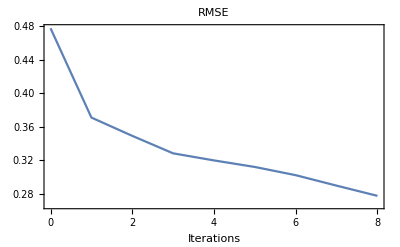

{FeedForwardNet[{{w1,w2}},{AccumulatedIterations→8,CreationDate→{2022,12,14,17,29,13.13213},Neuron→Sigmoid,FixedParameters→None,OutputNonlinearity→Sigmoid,NumberOfInputs→4}],NeuralFitRecord[FeedForwardNet, {ReportFrequency → 1, CriterionValues → {-values-}, CriterionValidationValues → {-values-}, ParameterRecord → {-parameters-}}]}

```mathematica
{fdfrwrd2,fitrecord}=NeuralFit[fdfrwrd,x,y,8]
```

```mathematica
NetPlot[fdfrwrd2,x,y,DataFormat->BarChart,OutputNonlinearity->UnitStep]
```

-Graphics3D-

```mathematica
Round@fdfrwrd2[x]-y
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,-1,1},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(*Our training looks good with only one error*)
```

```mathematica
(*As seen there is one training error lets take more information about this data*)
```

```mathematica
Position[Round@fdfrwrd2[x]-y,{0,-1,1}]
```

{{59}}

```mathematica
(*We get its position*)
```

```mathematica
x[[59]]
```

{6.,2.7,5.1,1.6}

```mathematica
(*This is actual data that used on training at that particular order*)
```

```mathematica
y[[59]]
```

{0,1,0}

```mathematica
(*This is what it shuold classified as*)
```

```mathematica
Round@fdfrwrd2[x[[59]]]
```

{0,0,1}

```mathematica
(*This is how the algorithm classify it*)
```

```mathematica
1./Length[y]*100
```

0.952381

```mathematica
(*We have one training error as seen and the percantege is %0.0952381 for training data*)
```

```mathematica
Round@fdfrwrd2[xtest]-ytest
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,-1,1},{0,0,0},{0,0,0},{0,0,0},{0,-1,1},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(*We have couple error in testing data lets try to add more neurons and see the results*)
```

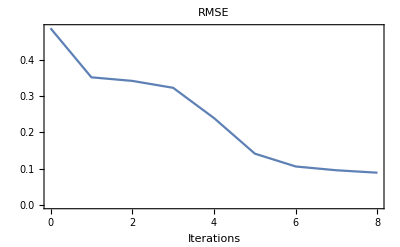

```mathematica
fdfrwrd=InitializeFeedForwardNet[x,y,{4},OutputNonlinearity->Sigmoid];
{fdfrwrd2,fitrecord}=NeuralFit[fdfrwrd,x,y,8];
```

```mathematica
Round@fdfrwrd2[xtest]-ytest
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,-1,1},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(*I can try to reduce the error with adding more neurons*)
```

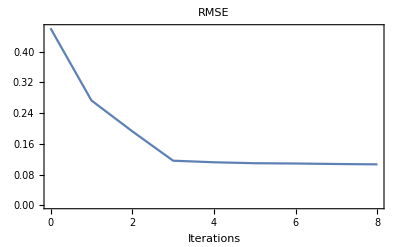

```mathematica
fdfrwrd=InitializeFeedForwardNet[x,y,{6},OutputNonlinearity->Sigmoid];
{fdfrwrd2,fitrecord}=NeuralFit[fdfrwrd,x,y,8];
```

```mathematica
Round@fdfrwrd2[xtest]-ytest
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,-1,1},{0,0,0},{0,0,0},{0,0,0},{0,-1,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,1,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(*It started overfitting so i will go with 4 neurons and 8 iterations *)
```

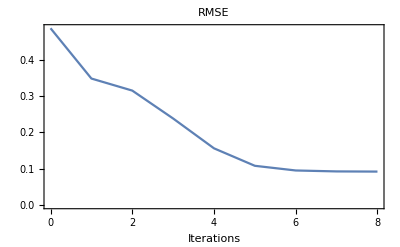

```mathematica
fdfrwrd=InitializeFeedForwardNet[x,y,{4},OutputNonlinearity->Sigmoid];
{fdfrwrd2,fitrecord}=NeuralFit[fdfrwrd,x,y,8];
```

```mathematica
Round@fdfrwrd2[xtest]-ytest
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,-1,1},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

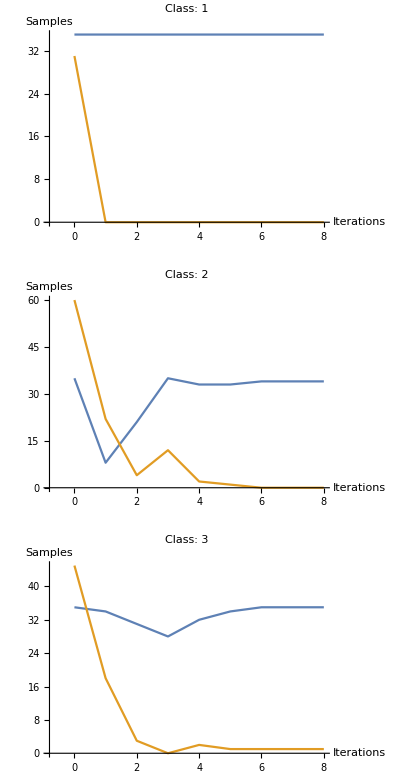

```mathematica
NetPlot[fitrecord,x,y,DataFormat->ClassPerformance,OutputNonlinearity->UnitStep]
```

```mathematica
NetPlot[fitrecord,x,y,DataFormat->BarChart,OutputNonlinearity->UnitStep,Intervals->4]
```

-Graphics-

```mathematica
Round@fdfrwrd2[xtest]-ytest
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,-1,1},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Position[Round@fdfrwrd2[xtest]-ytest,{0,-1,1}]
```

{{22}}

```mathematica
xtest[[22]]
```

{5.9,3.2,4.8,1.8}

```mathematica
Round@fdfrwrd2[xtest[[22]]]
```

{0,0,1}

```mathematica
1./Length[ytest]*100
```

2.22222

```mathematica
(*Our testing error is %2.222 which is pretty good i believe*)
```

```mathematica
Grid[{{15,0,0},{0,14,1},{0,0,15}}, Frame->All,Spacings->{2,0.5}]
```

15 | 0 | 0
0 | 14 | 1
0 | 0 | 15

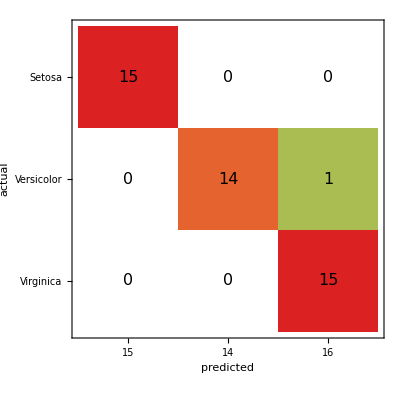

```mathematica
m={{15,0,0},{0,14,1},{0,0,15}};
k={"Setosa","Versicolor", "Virginica"};
MatrixPlot[m,ColorRules->{0->White},Frame->True,FrameLabel->{"actual","predicted"},FrameTicks->{{MapIndexed[{#2[[1]],#}&,k],MapIndexed[{#2[[1]],#}&,Total@Transpose@m]},{MapIndexed[{#2[[1]],#}&,Total[m]],MapIndexed[{#2[[1]],#}&,k]}},ColorFunction->"Rainbow",Epilog->MapIndexed[Text[Style[#,16],#2-1/2]&,Transpose@Reverse@m,{2}]]
```

```mathematica
(*This is our confisuon matrix using matrixplot*)
(*So for the last words. We trained the data and first i saw the training error was fine and i continued with it. Later when i test the data it had several errors. So i added one more neuron to reduce it. It worked for me with 4 neuron and 8 iterations. So after the changes i said maybe i can make %0 error percentage. But after adding more neurons i saw that it started overfitting. So i left it there. At the end my testing error was %2.222 which is pretty nice. I tried to automize the confisuon matrix but i couldn't manage to do it. Because i thought i have time until 19.12.2022. But i learned that i need to submit this task before the exam. Finally i actually find an piece of code from internet to make confisuon matrix seem better. I chaned some behaiovurs so my confision matrix was done. I learned a lot while doing the tasks. So thank you for it. I hope i didn't make any mistake. So that's all*)
```